Autor: Artur Bednarczyk

# Metody numeryczne w technice

## (kierunek informatyka)

## Projekt 9

Metoda odchyłek ważonych

Napisać procedurę realizującą metodę odchyłek ważonych dla równania:

u''(x)-3u'(x)=4x,   x∈(2,3),

z warunkami brzegowymi:

u(2)=0,
u(3)=0.

Przyjąć, że funkcje kształtu będą spełniały zadane warunki brzegowe.

a) Korzystając z napisanej procedury wyznaczyć metodą Galerkina rozwiązanie przybliżone przyjmując jako funkcje kształtu:

Φ_1(x)=(x-2)(x-3),   
Φ_2(x)=x(x-2)(x-3).

Na wspólnym rysunku wykreślić rozwiązanie dokładne oraz uzyskane rozwiązanie przybliżone. Policzyć także normę (w L^2) różnicy pomiędzy rozwiązaniem dokładnym i przybliżonym (wynik podać w postaci ułamka dziesiętnego).

b) Wykonać te same obliczenia dla trzech funkcji kształtu:

Φ_1(x)=(x-2)(x-3),   
Φ_2(x)=x(x-2)(x-3),   
Φ_3(x)=x^2(x-2)(x-3).

Na wspólnym rysunku wykreślić rozwiązanie dokładne oraz uzyskane rozwiązanie przybliżone. Policzyć także normę (w L^2) różnicy pomiędzy rozwiązaniem dokładnym i przybliżonym (wynik podać w postaci ułamka dziesiętnego).

## Rozwiązanie

Rozwiązanie przybliżone: 4/69 (-834+1205 x-564 x^2+85 x^3)

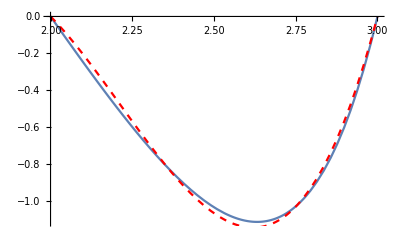

Norma L2: 0.000761936

Rozwiązanie przybliżone: 1/6 (516-892 x+597 x^2-182 x^3+21 x^4)

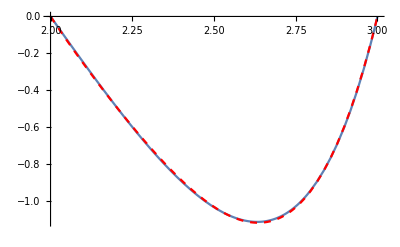

Norma L2: 0.0000148247

```mathematica
ClearAll["Global`*"];
(* Metoda Odchyłek Ważonych *)
mow1[a_,b_]:=Module[{
f1 = (x-2)(x-3),
f2 = x(x-2)(x-3),
result,T, r,e,res
},

T = Table[0,{i,1,3}];
e = Table[0, {i,1,2}];

T⟦1⟧ = p1*f1+p2*f2;
T⟦2⟧ = D[T⟦1⟧,x];
T⟦3⟧ = D[T⟦2⟧, x];

r =T⟦3⟧-3*T⟦2⟧-4x;
e⟦1⟧ =∫_a^b f1*rⅆx == 0;
e⟦2⟧=∫_a^b f2*rⅆx == 0;
result = Solve[e];
res = T⟦1⟧ /.{p1->result⟦1,1,2⟧, p2->result⟦1,2,2⟧};
Return[Simplify[res]];
];
mow2[a_,b_]:=Module[{
f1 = (x-2)(x-3),
f2 = x(x-2)(x-3),
f3 = x^2(x-2)(x-3),
result,T, r,e,res
},

T = Table[0,{i,1,3}];
e = Table[0, {i,1,3}];

T⟦1⟧ = p1*f1+p2*f2+p3*f3;
T⟦2⟧ = D[T⟦1⟧,x];
T⟦3⟧ = D[T⟦2⟧, x];

r =T⟦3⟧-3*T⟦2⟧-4x;
e⟦1⟧ =∫_a^b f1*rⅆx == 0;
e⟦2⟧=∫_a^b f2*rⅆx == 0;
e⟦3⟧ = ∫_a^b f3*rⅆx == 0;
result = Solve[e];
res = T⟦1⟧ /.{p1->result⟦1,1,2⟧, p2->result⟦1,2,2⟧, p3->result⟦1,3,2⟧};
Return[Simplify[res]];
]
(* Dane *)
a = 2;
b = 3;
(* Rozwiązanie dokładne *)
r = DSolveValue[{u''[x]-3u'[x]==4x, u[2]==0, u[3]==0}, u[x], x];
plotR = Plot[r, {x,a,b}];
(* Przykład A *)
res1 = mow1[a,b];
plotRes1 = Plot[res1, {x,a,b}, PlotStyle->{Red, Dashed}];
Print["Rozwiązanie przybliżone: ", res1];
Show[plotR, plotRes1]
(*Norma L2*)
normL2a = ∫_a^b (res1 - r)^2 ⅆx;
Print["Norma L2: ", N[normL2a]];
(* Przykład B *)
res2 = mow2[a,b];
plotRes2 = Plot[res2, {x,a,b}, PlotStyle->{Red, Dashed}];
Print["Rozwiązanie przybliżone: ", res2];
Show[plotR, plotRes2]
(*Norma L2*)
normL2b = ∫_a^b (res2 - r)^2 ⅆx;
Print["Norma L2: ", N[normL2b]];
```